## Nested delta shell approximation to exponential potential using Cullen’s formula n0 = # shells m = meson mass α = strength R0 = IR cutoff pcd = p Cot[δ]

```mathematica
ParallelEvaluate[$RecursionLimit=5500];
```

```mathematica
n0=5000;
(*m=1;*)
l=0;
V0M = 6.0;
R0 =25;
dR=R0/n0;
r[n_] = (n-1/2) dR;
g[n_] = V0M  E^(-r[n]) dR;
(*Clear[ψf,φ,ξ,Omat,gmat,mat,R,n]*)
Clear[ψf,φ,ξ,mat,R,n]
ξ[n_,k_]=k r[n];

mat[n_,k_]:=If[Abs[V0M]>=1,{{1/g[n]+ξ[n,k]*SphericalBesselJ[l,ξ[n,k]]*SphericalBesselY[l,ξ[n,k]],ξ[n,k]*(SphericalBesselY[l,ξ[n,k]])^2},{-ξ[n,k]*(SphericalBesselJ[l,ξ[n,k]])^2,1/g[n]-ξ[n,k]*SphericalBesselJ[l,ξ[n,k]]*SphericalBesselY[l,ξ[n,k]]}} ,{{1+g[n]*ξ[n,k]*SphericalBesselJ[l,ξ[n,k]]*SphericalBesselY[l,ξ[n,k]],g[n]*ξ[n,k]*(SphericalBesselY[l,ξ[n,k]])^2},{-g[n]*ξ[n,k]*(SphericalBesselJ[l,ξ[n,k]])^2,1-g[n]*ξ[n,k]*SphericalBesselJ[l,ξ[n,k]]*SphericalBesselY[l,ξ[n,k]]}}];

φ[0,k_]={1,0}; (*May be adjusted for a different Boundary condition*)
φ[n_,k_]:=mat[n,k].φ[n-1,k];
ψf[k_]:=φ[n0,k];
pcd[k_]:=(η =ψf[k]; -k η[[1]]/η[[2]])
EFE[k_]:=pcd[k]*k^(2l);

YukBd[α_,η_,l_,x_]:=WhittakerM[I*α/2*1/Sqrt[α+η^2],l+1/2,2I*Sqrt[α+η^2]*x];
DYukBd[α_,η_,l_,x_]:=D[YukBd[α,η,l,y],y]/.y->x;

Solver3[η_,l_,α_,x0_]:=Module[{Sol,ϕ,x1,x2,Smat},
Sol=NDSolve[{SetPrecision[ϕ''[x]+(η^2-l(l+1)/x^2-α*Exp[-x]/x)*ϕ[x],15]==0,ϕ[x0]==SetPrecision[YukBd[α,η,l,x0],15],ϕ'[x0]==SetPrecision[DYukBd[α,η,l,x0],15]},ϕ[x],{x,x0,100/Abs[η]},WorkingPrecision->15][[1]][[1]][[2]];
ϕ[y_]:=Sol/.{x->y};
x1=90/η;
x2=x1+1/(2η);
(*Smat1=(-1)^l*(Exp[-I*η*x2]*ϕ[x1]-Exp[-I*η*x1]ϕ[x2])/(Exp[I*η*x2]*ϕ[x1]-Exp[I*η*x1]ϕ[x2]);
Smat2=Exp[2I*ArcCot[1/η*ϕ'[q]/ϕ[q]]]/.q->Pi*(31+l/2)/η;*);
Smat4=-((ϕ[f]*D[p*SphericalHankelH2[l,p],p]-ϕ'[f]*p/η*SphericalHankelH2[l,p])/(ϕ[f]*D[p*SphericalHankelH1[l,p],p]-ϕ'[f]*p/η*SphericalHankelH1[l,p]))/.{p->90,f->90/η};
(*Smat3=-Wronskian[{ψ[f],SphericalHankelH2[l,f]},f]/Wronskian[{ψ[f],SphericalHankelH1[l,f]},f]/.{f->90/Abs[η]}*)
Smat4]
```

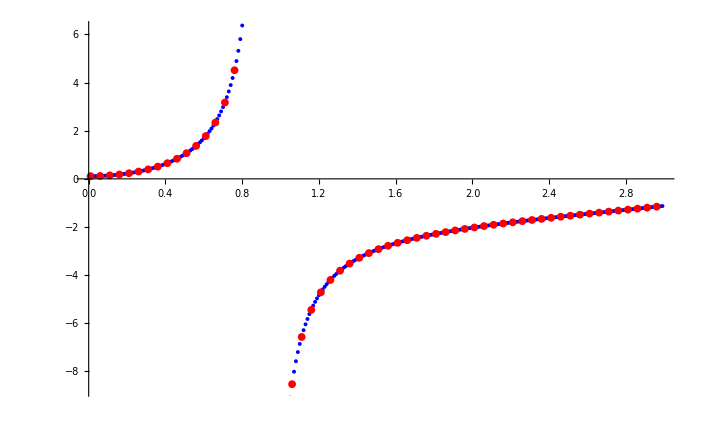

```mathematica
Momentum=Range[0.00001`15,3.0`15,0.01`15];
Momentum2=Range[0.01`15,3.0,0.05`15];
VALS=ParallelTable[(F=Solver3[h,l,-V0M,0.01];h^(2*l+1)*I*(F+1)/(F-1)),{h,Momentum}];
VALS2=ParallelTable[EFE[h],{h,Momentum2}];
(*VALS1=ParallelTable[(F=Solver3[h,l,-15.00,0.01];Arg[F[[3]]]/2),{h,Momentum}];*)
ListPlot[{Transpose[{Momentum,Re[VALS]}],Transpose[{Momentum2,Re[VALS2]}]},PlotStyle->{Directive[Blue,PointSize[0.004]],Directive[Red, PointSize[0.008]]},PlotRange->Automatic]
```

```mathematica
ListPlot3D[Flatten[ParallelTable[{x,y,EFE[x+I*y]},{x,-3.018,3.012,.9143},{y,-3.01,3.01,.9143}],1]]
```

```mathematica
pcd[-3.3`15*I]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Indeterminate

```mathematica
Momentum3=Range[0.001*I,1.0*I,0.01*I];
VALS3=ParallelTable[pcd[h]-I*h,{h,Momentum3}];
```

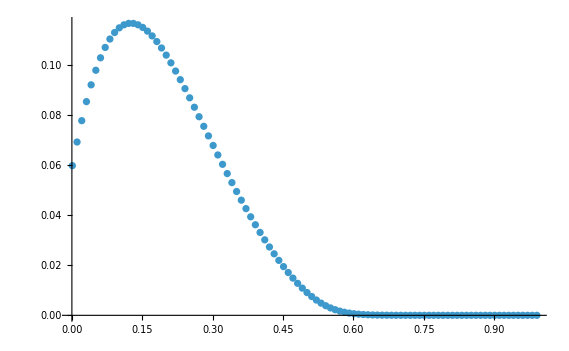

```mathematica
ListPlot[Transpose[{Abs[Momentum3],Abs[VALS3]}],PlotRange->Automatic]
```

```mathematica
(*GeneralizedLaguerreQuadrature[f_,p_,n_:20,ϵ_:0.01]:=Module[{α,nodes,weights,result,poly,i},α=-p+ϵ;
poly=LaguerreL[n,α,x];
nodes=x/. NSolve[poly==0,x,Reals];
weights=Table[Gamma[n+α+1]/(n!*nodes[[i]]*LaguerreL[n-1,α+1,nodes[[i]]]^2),{i,n}];
result=Total[Table[weights[[i]]*nodes[[i]]^(-α-p)*f[nodes[[i]]],{i,n}]];
result]*)
```

```mathematica
(*Veff[x_,l_,γ_,α_,x0_]:=Piecewise[{{-γ^2+l*(l+1)/x^2,x<x0},{l*(l+1)/x^2+α*(.0/x^3+.0/x^2+1/x)*Exp[-x],x>=x0}}]
η=0.01`15;
l=1;
α=-2;
x0=0.1;
γ=1;
Sol=NDSolve[{ϕ''[x]+(η^2-Veff[x,l,γ,α,x0])*ϕ[x]==0,ϕ[0.001]==0.001*SphericalBesselJ[l,Sqrt[η^2+γ^2]*0.001],ϕ'[0.001]==SphericalBesselJ[l,Sqrt[η^2+γ^2]*0.001]+Sqrt[η^2+γ^2]*0.001*D[SphericalBesselJ[l,y],y]/.{y->Sqrt[η^2+γ^2]*0.001}},ϕ,{x,x0,50/Abs[η]}];
ysol=ϕ/.First[Sol]*)
```

```mathematica
(*Solver[η_,l_,γ_,α_,x0_]:=Module[{Sol,ϕ,x1,x2,Smat},Sol=NDSolve[{SetPrecision[ϕ''[x]+(η^2-Veff[x,l,γ,α,x0])*ϕ[x],15]==0,ϕ[x0]==SetPrecision[x0*SphericalBesselJ[l,Sqrt[η^2+γ^2]*x0],15],ϕ'[x0]==SetPrecision[SphericalBesselJ[l,Sqrt[η^2+γ^2]*x0]+Sqrt[η^2+γ^2]*x0*D[SphericalBesselJ[l,y],y]/.{y->Sqrt[η^2+γ^2]*x0},15]},ϕ[x],{x,x0,100/Abs[η]},WorkingPrecision->15][[1]][[1]][[2]];
ϕ[y_]:=Sol/.{x->y};
x1=99/Abs[η];
x2=x1+5/(10*Abs[η]);
Smat=(-1)^l*(Exp[-I*η*x2]*ϕ[x1]-Exp[-I*η*x1]ϕ[x2])/(Exp[I*η*x2]*ϕ[x1]-Exp[I*η*x1]ϕ[x2]);
Smat]*)
```

```mathematica
(*Veff2[u_,l_,γ_,α_,x0_,η_]:=Piecewise[{{-γ^2/η^2+l*(l+1)/u^2,u<η*x0},{l*(l+1)/u^2+α*(0η^2/u^2+0η/u+1)*Exp[-u/η]/(u*η),u>=η*x0}}]
Solver2[η_,l_,γ_,α_,x0_]:=Module[{Sol,ϕ,x1,x2,xr,Smat},
xr=η*x0/10;
Sol=NDSolve[{SetPrecision[ϕ''[u]+(1-Veff2[u,l,γ,α,x0,η])*ϕ[u],15]==0,ϕ[xr]==SetPrecision[xr*SphericalBesselJ[l,Sqrt[1+γ^2/η^2]*xr],15],ϕ'[xr]==SetPrecision[SphericalBesselJ[l,Sqrt[1+γ^2/η^2]*xr]+Sqrt[1+γ^2/η^2]*xr*D[SphericalBesselJ[l,y],y]/.{y->Sqrt[1+γ^2/η^2]*xr},15]},ϕ[u],{u,xr,500},WorkingPrecision->15][[1]][[1]][[2]];
ϕ[y_]:=Sol/.{u->y};
x1=499;
x2=x1+1/2;
Smat=(-1)^l*(Exp[-I*x2]*ϕ[x1]-Exp[-I*x1]ϕ[x2])/(Exp[I*x2]*ϕ[x1]-Exp[I*x1]ϕ[x2]);
Smat]*)
```

```mathematica
Timing[Solver3[0.02`15,1,-1,0.01]]
```

{0.151454,-0.49689186062+0.86781246756 ⅈ}

```mathematica
Momentum=Range[0.00001`15,3.0`15,0.01`15];
VALS1=ParallelTable[(F=Solver3[h,l,-V0M,0.01];Arg[F[[2]]]/2),{h,Momentum}];
```

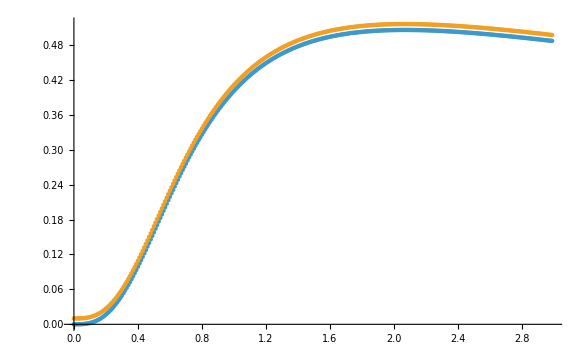

```mathematica
ListPlot[{Transpose[{Momentum,Re[VALS]}],Transpose[{Momentum,Re[VALS1]}]},PlotRange->Automatic]
```